```mathematica
(***Note: Values for generating these plots are embedded within the raw data set, which is too large to upload onto the public data repository***)
```

```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
controlColor=Black;
```

```mathematica
(*************************)
```

```mathematica
dateMouseListControl={{"012122","Mouse22550"},{"012822","Mouse22549"},{"121621","Mouse22525"},{"121721","Mouse22599"},{"011122","Mouse22598"},{"032923","Mouse23149"},{"033023","Mouse23128"},{"033123","Mouse23149"},{"070323","Mouse23149"},{"070423","Mouse23128"},{"070723","Mouse23128"}};
```

```mathematica
(***V1 axons, eOPN3***)
```

```mathematica
dateMouseListV1axons={{"012722","Mouse22504"},{"121821","Mouse22485"},{"062723","Mouse23154"},{"062723","Mouse23182"},{"063023","Mouse23154"},{"063023","Mouse23182"}};
```

```mathematica
(***LP axons, eOPN3***)
```

```mathematica
dateMouseListLPaxons={{"050123","Mouse23133"},{"050123","Mouse23142"},{"050323","Mouse23133"},{"050323","Mouse23142"},{"051823","Mouse23198"},{"052623","Mouse23198"},{"052623","Mouse23105"},{"062923","Mouse23139"},{"070223","Mouse23139"}};
```

```mathematica
(***LM axons, eOPN3***)
```

```mathematica
dateMouseListLMaxons={{"062623","Mouse23152"},{"062823","Mouse23152"},{"062923","Mouse23190"},{"070123","Mouse23190"},{"070723","Mouse23666"},{"071223","Mouse23666"}};
```

```mathematica
(*******************************)
```

```mathematica
pairedROIsListControl=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/PairedAnalysis/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_pairedROIsPupil.txt"],"List"],{n,1,Length[dateMouseListControl]}];
```

```mathematica
pairedROIsListV1axons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/PairedAnalysis/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_pairedROIsPupil.txt"],"List"],{n,1,Length[dateMouseListV1axons]}];
```

```mathematica
pairedROIsListLPaxons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/PairedAnalysis/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_pairedROIsPupil.txt"],"List"],{n,1,Length[dateMouseListLPaxons]}];
```

```mathematica
pairedROIsListLMaxons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/PairedAnalysis/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_pairedROIsPupil.txt"],"List"],{n,1,Length[dateMouseListLMaxons]}];
```

```mathematica
(*******************************)
```

```mathematica
pupilCCControlDark=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/","Session1","/Pupil/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_","Session1","_","dFFpupilCrossCorr_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListControl[[n]]}],{n,1,Length[dateMouseListControl]}];
```

```mathematica
pupilCCControlLED=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/","Session2","/Pupil/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_","Session2","_","dFFpupilCrossCorr_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListControl[[n]]}],{n,1,Length[dateMouseListControl]}];
```

```mathematica
pupilCCV1axonsDark=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/","Session1","/Pupil/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_","Session1","_","dFFpupilCrossCorr_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListV1axons[[n]]}],{n,1,Length[dateMouseListV1axons]}];
```

```mathematica
pupilCCV1axonsLED=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/","Session2","/Pupil/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_","Session2","_","dFFpupilCrossCorr_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListV1axons[[n]]}],{n,1,Length[dateMouseListV1axons]}];
```

```mathematica
pupilCCLPaxonsDark=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/","Session1","/Pupil/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_","Session1","_","dFFpupilCrossCorr_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListLPaxons[[n]]}],{n,1,Length[dateMouseListLPaxons]}];
```

```mathematica
pupilCCLPaxonsLED=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/","Session2","/Pupil/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_","Session2","_","dFFpupilCrossCorr_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListLPaxons[[n]]}],{n,1,Length[dateMouseListLPaxons]}];
```

```mathematica
pupilCCLMaxonsDark=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/","Session1","/Pupil/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_","Session1","_","dFFpupilCrossCorr_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListLMaxons[[n]]}],{n,1,Length[dateMouseListLMaxons]}];
```

```mathematica
pupilCCLMaxonsLED=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/","Session2","/Pupil/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_","Session2","_","dFFpupilCrossCorr_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListLMaxons[[n]]}],{n,1,Length[dateMouseListLMaxons]}];
```

```mathematica
catenatedPupilCCControlDark=Flatten[pupilCCControlDark,1];
```

```mathematica
catenatedPupilCCControlLED=Flatten[pupilCCControlLED,1];
```

```mathematica
catenatedPupilCCV1axonsDark=Flatten[pupilCCV1axonsDark,1];
```

```mathematica
catenatedPupilCCV1axonsLED=Flatten[pupilCCV1axonsLED,1];
```

```mathematica
catenatedPupilCCLPaxonsDark=Flatten[pupilCCLPaxonsDark,1];
```

```mathematica
catenatedPupilCCLPaxonsLED=Flatten[pupilCCLPaxonsLED,1];
```

```mathematica
catenatedPupilCCLMaxonsDark=Flatten[pupilCCLMaxonsDark,1];
```

```mathematica
catenatedPupilCCLMaxonsLED=Flatten[pupilCCLMaxonsLED,1];
```

```mathematica
(**************)
```

```mathematica
(***)
```

```mathematica
meanCatenatedPupilCCControlDark=Mean[catenatedPupilCCControlDark];
```

```mathematica
semCatenatedPupilCCControlDark=(#/Sqrt@Length[catenatedPupilCCControlDark])&/@StandardDeviation[catenatedPupilCCControlDark];
```

```mathematica
(***)
```

```mathematica
meanCatenatedPupilCCV1axonsDark=Mean[catenatedPupilCCV1axonsDark];
```

```mathematica
semCatenatedPupilCCV1axonsDark=(#/Sqrt@Length[catenatedPupilCCV1axonsDark])&/@StandardDeviation[catenatedPupilCCV1axonsDark];
```

```mathematica
(***)
```

```mathematica
meanCatenatedPupilCCLPaxonsDark=Mean[catenatedPupilCCLPaxonsDark];
```

```mathematica
semCatenatedPupilCCLPaxonsDark=(#/Sqrt@Length[catenatedPupilCCLPaxonsDark])&/@StandardDeviation[catenatedPupilCCLPaxonsDark];
```

```mathematica
(***)
```

```mathematica
meanCatenatedPupilCCLMaxonsDark=Mean[catenatedPupilCCLMaxonsDark];
```

```mathematica
semCatenatedPupilCCLMaxonsDark=(#/Sqrt@Length[catenatedPupilCCLMaxonsDark])&/@StandardDeviation[catenatedPupilCCLMaxonsDark];
```

```mathematica
(***)
```

```mathematica
meanCatenatedPupilCCControlLED=Mean[catenatedPupilCCControlLED];
```

```mathematica
semCatenatedPupilCCControlLED=(#/Sqrt@Length[catenatedPupilCCControlLED])&/@StandardDeviation[catenatedPupilCCControlLED];
```

```mathematica
(***)
```

```mathematica
meanCatenatedPupilCCV1axonsLED=Mean[catenatedPupilCCV1axonsLED];
```

```mathematica
semCatenatedPupilCCV1axonsLED=(#/Sqrt@Length[catenatedPupilCCV1axonsLED])&/@StandardDeviation[catenatedPupilCCV1axonsLED];
```

```mathematica
(***)
```

```mathematica
meanCatenatedPupilCCLPaxonsLED=Mean[catenatedPupilCCLPaxonsLED];
```

```mathematica
semCatenatedPupilCCLPaxonsLED=(#/Sqrt@Length[catenatedPupilCCLPaxonsLED])&/@StandardDeviation[catenatedPupilCCLPaxonsLED];
```

```mathematica
(***)
```

```mathematica
meanCatenatedPupilCCLMaxonsLED=Mean[catenatedPupilCCLMaxonsLED];
```

```mathematica
semCatenatedPupilCCLMaxonsLED=(#/Sqrt@Length[catenatedPupilCCLMaxonsLED])&/@StandardDeviation[catenatedPupilCCLMaxonsLED];
```

```mathematica
(**************)
```

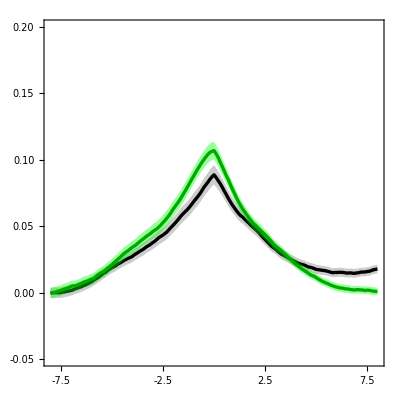

```mathematica
Show[ListLinePlot[{Part[#,2]&/@meanCatenatedPupilCCControlDark,Part[#,2]&/@meanCatenatedPupilCCControlDark+(Part[#,2]&/@semCatenatedPupilCCControlDark),Part[#,2]&/@meanCatenatedPupilCCControlDark-(Part[#,2]&/@semCatenatedPupilCCControlDark)},Filling->{1->{{2},Directive[Opacity[0.4],Gray]},1->{{3},Directive[Opacity[0.4],Gray]}},PlotStyle->{{Black,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.05,0.2}},FrameTicks->{{LinTicks[-0.05,0.2,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],ListLinePlot[{Part[#,2]&/@meanCatenatedPupilCCControlLED,Part[#,2]&/@meanCatenatedPupilCCControlLED+(Part[#,2]&/@semCatenatedPupilCCControlLED),Part[#,2]&/@meanCatenatedPupilCCControlLED-(Part[#,2]&/@semCatenatedPupilCCControlLED)},Filling->{1->{{2},Directive[Opacity[0.4],Green]},1->{{3},Directive[Opacity[0.4],Green]}},PlotStyle->{{Darker@Green,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.05,0.2}},FrameTicks->{{LinTicks[-0.05,0.2,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],AspectRatio->1]
```

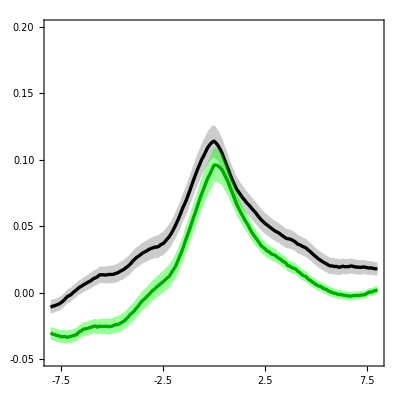

```mathematica
Show[ListLinePlot[{Part[#,2]&/@meanCatenatedPupilCCV1axonsDark,Part[#,2]&/@meanCatenatedPupilCCV1axonsDark+(Part[#,2]&/@semCatenatedPupilCCV1axonsDark),Part[#,2]&/@meanCatenatedPupilCCV1axonsDark-(Part[#,2]&/@semCatenatedPupilCCV1axonsDark)},Filling->{1->{{2},Directive[Opacity[0.4],Gray]},1->{{3},Directive[Opacity[0.4],Gray]}},PlotStyle->{{Black,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.05,0.2}},FrameTicks->{{LinTicks[-0.05,0.2,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],ListLinePlot[{Part[#,2]&/@meanCatenatedPupilCCV1axonsLED,Part[#,2]&/@meanCatenatedPupilCCV1axonsLED+(Part[#,2]&/@semCatenatedPupilCCV1axonsLED),Part[#,2]&/@meanCatenatedPupilCCV1axonsLED-(Part[#,2]&/@semCatenatedPupilCCV1axonsLED)},Filling->{1->{{2},Directive[Opacity[0.4],Green]},1->{{3},Directive[Opacity[0.4],Green]}},PlotStyle->{{Darker@Green,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.05,0.2}},FrameTicks->{{LinTicks[-0.05,0.2,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],AspectRatio->1]
```

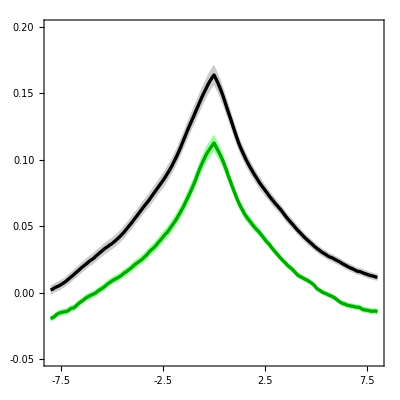

```mathematica
Show[ListLinePlot[{Part[#,2]&/@meanCatenatedPupilCCLPaxonsDark,Part[#,2]&/@meanCatenatedPupilCCLPaxonsDark+(Part[#,2]&/@semCatenatedPupilCCLPaxonsDark),Part[#,2]&/@meanCatenatedPupilCCLPaxonsDark-(Part[#,2]&/@semCatenatedPupilCCLPaxonsDark)},Filling->{1->{{2},Directive[Opacity[0.4],Gray]},1->{{3},Directive[Opacity[0.4],Gray]}},PlotStyle->{{Black,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.05,0.2}},FrameTicks->{{LinTicks[-0.05,0.2,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],ListLinePlot[{Part[#,2]&/@meanCatenatedPupilCCLPaxonsLED,Part[#,2]&/@meanCatenatedPupilCCLPaxonsLED+(Part[#,2]&/@semCatenatedPupilCCLPaxonsLED),Part[#,2]&/@meanCatenatedPupilCCLPaxonsLED-(Part[#,2]&/@semCatenatedPupilCCLPaxonsLED)},Filling->{1->{{2},Directive[Opacity[0.4],Green]},1->{{3},Directive[Opacity[0.4],Green]}},PlotStyle->{{Darker@Green,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.05,0.2}},FrameTicks->{{LinTicks[-0.05,0.2,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],AspectRatio->1]
```

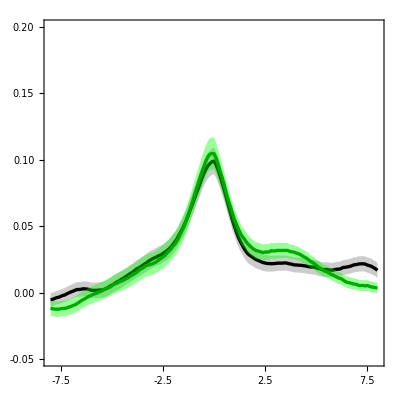

```mathematica
Show[ListLinePlot[{Part[#,2]&/@meanCatenatedPupilCCLMaxonsDark,Part[#,2]&/@meanCatenatedPupilCCLMaxonsDark+(Part[#,2]&/@semCatenatedPupilCCLMaxonsDark),Part[#,2]&/@meanCatenatedPupilCCLMaxonsDark-(Part[#,2]&/@semCatenatedPupilCCLMaxonsDark)},Filling->{1->{{2},Directive[Opacity[0.4],Gray]},1->{{3},Directive[Opacity[0.4],Gray]}},PlotStyle->{{Black,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.05,0.2}},FrameTicks->{{LinTicks[-0.05,0.2,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],ListLinePlot[{Part[#,2]&/@meanCatenatedPupilCCLMaxonsLED,Part[#,2]&/@meanCatenatedPupilCCLMaxonsLED+(Part[#,2]&/@semCatenatedPupilCCLMaxonsLED),Part[#,2]&/@meanCatenatedPupilCCLMaxonsLED-(Part[#,2]&/@semCatenatedPupilCCLMaxonsLED)},Filling->{1->{{2},Directive[Opacity[0.4],Green]},1->{{3},Directive[Opacity[0.4],Green]}},PlotStyle->{{Darker@Green,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.05,0.2}},FrameTicks->{{LinTicks[-0.05,0.2,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],AspectRatio->1]
```